## 1 Import Data, CD Algorithm via Edge Betweenness

```mathematica
data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21\\All Spins\\F21SpinsExpressionPerStudentResults.xlsx"][[1]];  (* imports the per-student expression results excel file *)
SetDirectory[NotebookDirectory[]]; 

For[i=1,i≤Dimensions[data][[1]],i++, (* this loop turns all of the weights into integers.  This is necessary to make the weights -> # of links *)
data[[i]][[3]]=Round[data[[i]][[3]]]
]

(* this block is just extracting all of the info from the imported file, as well as naming the vertices *)
vertices={
Property["a",VertexLabels->OverVector["v"]],
Property["b",VertexLabels->OverHat["j"]],
Property["c",VertexLabels->OverHat["S_z"]],
Property["d",VertexLabels->"f(x)"],
Property["e",VertexLabels->"|ψ⟩"],
Property["f",VertexLabels->"|E_2⟩"],
Property["g",VertexLabels->"⟨E_1|"],
Property["h",VertexLabels->"ψ(x)"],
Property["i",VertexLabels->"ψ^*(x)"],
Property["j",VertexLabels->"φ_3(x)"],
Property["k",VertexLabels->"φ_4^*(x)"],
Property["l",VertexLabels->OverVector["u"]·OverVector["v"]],
Property["m",VertexLabels->"⟨ψ|ψ⟩"],
Property["n",VertexLabels->"⟨E_3|ψ⟩"],
Property["o",VertexLabels->"∫ψ^*ψdx"],
Property["p",VertexLabels->"∫φ_1^*ψdx"],
Property["q",VertexLabels->"|⟨E_4|ψ⟩|^2"],
Property["r",VertexLabels->"|∫ψ^*ψdx|^2"],
Property["s",VertexLabels->"|∫φ_2^*ψdx|^2"],
Property["t",VertexLabels->"⟨ψ|"]
};

vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};
edges=Table[data[[i,1]]<->data[[i,2]],{i,1,Length[data]}];
edgeweights=Table[data[[i,3]],{i,1,Length[data]}];

(* here I create another version of edgeweights, but one that I will not change throughout the algorithm, just so I can see what the weights are even after the algorithm has run *)
weights=Table[data[[i,3]],{i,1,Length[data]}];

(* creates a basic graph of the network *)
g=Graph[vertices,edges,EdgeWeight->edgeweights];

a=WeightedAdjacencyMatrix[g];
G=AdjacencyGraph[vertices,a]; (* this block turns the weights into # of links *)

HighlightGraph[g,VertexList[g],VertexSize->Thread[VertexList[g]->Rescale[BetweennessCentrality[g]]]];

wcent=EdgeBetweennessCentrality[g]/edgeweights;  (* creates the centrality weights for all of the edges in the network. The reason for the division by the edgeweights is because we are treating each edge with more than one weight as multiple edges (as many edges as they are weighted by). This means that their betweenness should be reduced by that factor, as a more weighted connection should be less likely to be removed.  This is just initializing it for the original network. As the later for loop goes on, it will be updated to *)

(* defines num and numVerts as the number of edges (and therefore total cuts) and vertices, respectively *)
num=Dimensions[edgeweights][[1]];
numVerts=Dimensions[vertices][[1]];

(* initializes a list that will keep track of the edges that are removed, as well as in what order they were removed *)
removeList=Table[0,num];

(* creates the same graph as the per-student expression network code does, including the coloring *)
shapeFunc=With[{weight=PropertyValue[{g,#2},EdgeWeight]},{AbsoluteThickness[weight],Hue[weight/32.,1,1],Line@#1}]&;
Graph[vertices,edges,EdgeWeight->edgeweights,EdgeShapeFunction->shapeFunc,VertexSize->Medium,VertexLabelStyle->32];

tlG=Table[0,num];  (* initializes the timelapse table that will be filled with the frames of the timelapse animation *)
tlGraphs=Table[0,num];  (* initializes the timelapse table that will be filled with the frames of the timelapse animation.  THIS NOW INCLUDES HIGHLIGHTING THE HIGHEST CENTRALITY EDGE *)
tlGraphs1=Table[0,num]; (* same as other one, but this one is for the colorized timelapse *)
tlGraphs2=Table[0,num]; (* same as tlGraphs1, but without resizing the vertices *)
tlGraphs3=Table[0,num];
tlGraphs4=Table[0,num];
tlGraphs5=Table[0,num];

centralityTable=Table[0,num,numVerts];  (* initializes the table for storing the centrality scores for each vertex as the network is pared down *)
highCentralityList=Table[0,num];  (* initializes the list for storing which edge is deleted for each step, for the purposes of highlighting them before they are removed *)

(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]

(* This for loop generates the timelapses by calculating the betweenness centrality for each edge in the network, deleting the edge with the highest betweenness, and then recalculating betweennesses for the new network *)
For[i=1,i<=num,i++,
centralityTable[[i]]=BetweennessCentrality[g];  (* records the centralities of vertices in the graph at this point in the algorithm.  THIS ISN'T USED LATER *)
pos=Ordering[wcent,-1];  (* gives the position of the current largest betweenness within the wcent list *)
highCentralityList[[i]]=EdgeList[g][[pos[[]]]];  (* records the edges that are removed, in the order in which they are removed *)
removeList[[i]]=pos[[1]];  (* adds the position of the current largest betweenness to the "removeList" list, so we can keep track of which edges have been removed and in what order *)

(* fills up tlGraph list with each graph, so I can generate a timelapse of the splitting *)
tlG[[i]]=Graph[vertices,edges,EdgeWeight->edgeweights,VertexSize->Medium,VertexLabelStyle->30,ImageSize->Large];
(*
tlGraphs[[i]]=HighlightGraph[tlG[[i]],{Style[highCentralityList[[i]][[1]]]}];  
*)
tlGraphs[[i]]=tlG[[i]];
vd=VertexDegree[tlGraphs[[i]]];  (* assigns (and reassigns on each loop) vd to be a list of the vertex degrees. This will be used for coloring (and maybe sizing) the vertices *)

(* generates list of graphs with colors added to the vertices/edges. tlGraphs1 includes larger vertices, for looking at, while tlGraphs2 is intended for GIFs (smaller vertices) *)
tlGraphs1[[i]]=SetProperty[tlGraphs[[i]],{
VertexSize->Thread[VertexList[tlGraphs[[i]]]->.6N[.1+Rescale[vd]]^.5],
VertexStyle->Thread[VertexList[tlGraphs[[i]]]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[vd])],
EdgeStyle->Thread[EdgeList[tlGraphs[[i]]]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeweights])]
}];
tlGraphs2[[i]]=SetProperty[tlGraphs[[i]],{
VertexStyle->Thread[VertexList[tlGraphs[[i]]]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[vd])],
EdgeStyle->Thread[EdgeList[tlGraphs[[i]]]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeweights])]
}];

(* generates a list of graphs that is tlGraphs2, but with the highest-betweenness edge having no color/thickness applied.  Intended to highlight which edge is next to be removed *)
tlGraphs3[[i]]=SetProperty[tlGraphs[[i]],{
VertexStyle->Thread[VertexList[tlGraphs[[i]]]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[vd])],
EdgeStyle->Thread[Delete[EdgeList[tlGraphs[[i]]],Position[EdgeList[tlGraphs[[i]]],highCentralityList[[i]][[1]]][[1]][[1]]]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[Delete[edgeweights,Position[EdgeList[tlGraphs[[i]]],highCentralityList[[i]][[1]]][[1]][[1]]]])]
}];

tlGraphs4[[i]]=HighlightGraph[tlGraphs[[i]],highCentralityList[[i]]];

tlGraphs5[[i]]=SetProperty[
tlGraphs[[i]],{
VertexStyle->Thread[VertexList[tlGraphs[[i]]]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[vd])],
VertexCoordinates->circle[20],
EdgeStyle->Thread[EdgeList[tlGraphs[[i]]]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeweights])]
}];

(* removes the edge and other necessary stuff tied to it from relevant lists *)
wcent=Delete[wcent,pos[[1]]];
edges=Delete[edges,pos[[1]]];
edgeweights=Delete[edgeweights,pos[[1]]];

(* updates g with the new graphs as edges are being removed.  This is necessary, as g is used to calculate the betweennesses at the beginning of every loop *)
g=Graph[vertices,edges,EdgeWeight->edgeweights,EdgeShapeFunction->shapeFunc,VertexSize->Medium,VertexLabelStyle->32];(* add print to this if you want to see the timelapse graphs of the network dividing *)

(* recalculates the betweenness centralities for the now-one-edge-smaller graph *)
wcent=EdgeBetweennessCentrality[g]/edgeweights
]
```

## 2 Community Detection Animation

```mathematica
ListAnimate[tlGraphs,1,ImageSize->Automatic];  (* shows the evolution of the betweenness centrality splitting the network *)
ListAnimate[tlGraphs1,1,ImageSize->All];
ListAnimate[tlGraphs2,1,ImageSize->All];
ListAnimate[tlGraphs3,1,ImageSize->All];
ListAnimate[tlGraphs4,1,ImageSize->All];
```

## 3 Dendrogram

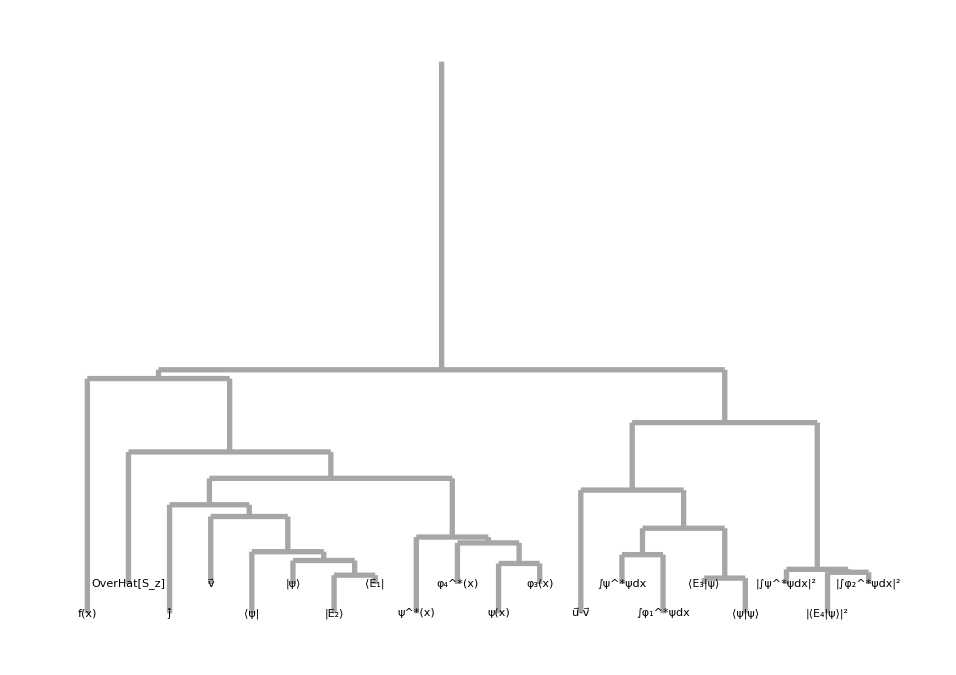

```mathematica
ConnectedGraphComponents[tlGraphs3[[150]]];
Length@ConnectedGraphComponents[tlGraphs3[[150]]];

(* initializes nComm as the number of disconnected subgraphs in the original, full network.  This will be updated in the loop to always be the current number of disconnected subgraphs *)
nComm=Length@ConnectedGraphComponents[tlGraphs3[[1]]];

(* redundant--I had forgotten that "num" was already used earlier for the number of edges *)
nEdges=EdgeCount[tlGraphs3[[1]]];
(* initializes splits as an empty list *)
splits={};

(* goes through the list of graphs as edges are removed, and adds the total number of removed edges at the point when a subgraph divides to the "splits" list.  This allows us to keep track of when the splits in the network occur, so we can more easily identify what spit off from where, and when that division occurs *)
For[i=1,i<=nEdges,i++,
j=nComm;
nComm=Length@ConnectedGraphComponents[tlGraphs3[[i]]];
If[j!=nComm,
splits=Append[splits,i]
]
]

(* initializes splitGraphs as an empty list, to be filled with the graphs *right before* being divided *)
splitGraphs={};
splitNumGraphs={};

(* goes through and fills splitGraphs with snapshots of the network, right before each split occurs *)
For[i=1,i<=Length@splits,i++,
splitGraphs=Append[
splitGraphs,
Show[
(* because we're using tlGraphs3, AND we're looking at the networks one step before they are divided, we can see the edge that will be removed in that step (they are highlighted in tlGraphs3) *)
tlGraphs3[[splits[[i]]-1]],
Graphics[Text[Style[ToString[splits[[i]]-1],FontSize->50,Bold]]]
]
];
splitNumGraphs=Append[
splitNumGraphs,
Show[
(* because we're using tlGraphs3, AND we're looking at the networks one step before they are divided, we can see the edge that will be removed in that step (they are highlighted in tlGraphs3) *)
tlGraphs3[[splits[[i]]-1]],
Graphics[Text[Style[ToString[i],FontSize->30,Bold]]]
]
]
]

(* required to have a vertex for each division point of the graph (nineteen), as well as each expression *)treeVerts={"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19",OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|","0"};



(* NEED TO GO THROUGH THE TREEEDGES AND FILL IN THE CORRECT LINKS FROM THE UPDATED DENDROGRAM *)




(* unfortunately, this is required to be filled out manually, by creating the dendrogram on paper, and noting when and where each division takes place.  Not fun. *)
treeEdges={treeVerts[[40]]<->treeVerts[[1]],treeVerts[[1]]<->treeVerts[[2]],treeVerts[[1]]<->treeVerts[[3]],treeVerts[[2]]<->treeVerts[[23]],treeVerts[[2]]<->treeVerts[[4]],treeVerts[[3]]<->treeVerts[[6]],treeVerts[[3]]<->treeVerts[[16]],treeVerts[[4]]<->treeVerts[[22]],treeVerts[[4]]<->treeVerts[[5]],treeVerts[[5]]<->treeVerts[[7]],treeVerts[[5]]<->treeVerts[[10]],treeVerts[[6]]<->treeVerts[[31]],treeVerts[[6]]<->treeVerts[[9]],treeVerts[[7]]<->treeVerts[[21]],treeVerts[[7]]<->treeVerts[[8]],treeVerts[[8]]<->treeVerts[[20]],treeVerts[[8]]<->treeVerts[[12]],treeVerts[[9]]<->treeVerts[[13]],treeVerts[[9]]<->treeVerts[[19]],treeVerts[[10]]<->treeVerts[[28]],treeVerts[[10]]<->treeVerts[[11]],treeVerts[[11]]<->treeVerts[[30]],treeVerts[[11]]<->treeVerts[[15]],treeVerts[[12]]<->treeVerts[[39]],treeVerts[[12]]<->treeVerts[[14]],treeVerts[[13]]<->treeVerts[[34]],treeVerts[[13]]<->treeVerts[[35]],treeVerts[[14]]<->treeVerts[[24]],treeVerts[[14]]<->treeVerts[[18]],treeVerts[[15]]<->treeVerts[[27]],treeVerts[[15]]<->treeVerts[[29]],treeVerts[[16]]<->treeVerts[[37]],treeVerts[[16]]<->treeVerts[[17]],treeVerts[[17]]<->treeVerts[[36]],treeVerts[[17]]<->treeVerts[[38]],treeVerts[[18]]<->treeVerts[[25]],treeVerts[[18]]<->treeVerts[[26]],treeVerts[[19]]<->treeVerts[[33]],treeVerts[[19]]<->treeVerts[[32]]};

(* defines the weights of the vertices (which Mathematica uses as the "heights" of the division points when the tree graph is converted to a dendrogram)  The +1 is required because "splits" doesn't include the final division (for some reason) *)
heightStagger=Join[nEdges+1-splits,{0,-2,-12,-2,-12,-2,-12,-2,-12,-12,-2,-2,-12,-12,-2,-2,-12,-12,-2,-2,-12,nEdges}];
heightFlat=Join[nEdges+1-splits,{0},Table[-2,numVerts],{nEdges}];

TownsendTreeStagger=TreeGraph[treeVerts,treeEdges,VertexLabels->"Name",VertexWeight->heightStagger];
TownsendTreeFlat=TreeGraph[treeVerts,treeEdges,VertexLabels->"Name",VertexWeight->heightFlat];

Dendrogram[TownsendTreeStagger]/.Line[x_]:>{Thickness[0.005],Line[x]};
Dendrogram[TownsendTreeFlat]/.Line[x_]:>{Thickness[0.005],Line[x]};

Dendrogram[TownsendTreeStagger,ImageSize->800]/.Line[x_]:>{Thickness[0.004],Line[x]}

splitGraphs//MatrixForm;
```

## 4 Cophenetics

```mathematica
(* this section will find the cophenetic distance between every expression in dendrogram *)
(* the cophenetic distance is the height on a dendrogram at which two elements were last part of the same cluster *)

(* we will determine the cophenetic distances by first assigning weights to the treegraph's edges equal to the number of steps they represent.  This will be done by taking the difference between the weights of the vertices on either end of the edge.  Once we have a treegraph where the edgeweights correspond to the number of steps between the vertices, we will then add up all of the weights along the path between two expression vertices.  This should effectively be equal to double the cophenetic distance between those two vertices. *)

numTreeVerts= Length[VertexList[TownsendTreeFlat]];
VertexList[TownsendTreeFlat];

FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[27]],VertexList[TownsendTreeFlat][[20]]];

TownsendTreeFlat;

(* first, define the vertex weights as above, but setting the expressions' vertex weights to negative one *)
cophenVertexWeights=Join[nEdges+1-splits,{0},Table[-1,numVerts],{nEdges}];

(* initialize the matrix that will be filled with the edgeweights.  It will be zero if they don't connect directly. *)
cophenEdgeWeights=Table[0,numTreeVerts,numTreeVerts];

(* here we fill in the cophenEdgeWeights matrix with the number of steps between the different vertices on the treegraph.  If they are not connected directly on the treegraph, then the number is zero. *)
For[i=1,i<=numTreeVerts,i++,
For[j=1,j<=numTreeVerts,j++,
If[Length[FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[i]],VertexList[TownsendTreeFlat][[j]]]]==2,
cophenEdgeWeights[[i,j]]=Abs[cophenVertexWeights[[i]]-cophenVertexWeights[[j]]]
]
]
]

(* initializing the table that will be filled with the cophenetic distances between the expressions on the dendrogram *)
cophenDist=Table[0,numVerts,numVerts];

cophenEdgeWeights//MatrixForm;
cophenDist//MatrixForm;

FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[27]],VertexList[TownsendTreeFlat][[20]]];
Position[FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[27]],VertexList[TownsendTreeFlat][[20]]],"ψ(x)"][[1]][[1]];

For[i=1,i<=numVerts,i++,
For[j=1,j<=numVerts,j++,
For[k=1,k<=Length[FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[i+19]],VertexList[TownsendTreeFlat][[j+19]]]]-1,k++,
(* this can be difficult to parse.  I am adding up the weights of the edges along the path between the ith and jth expressions.  I do this by finding the position within the treeVerts list of the kth and k+1th vertices of the shortest path between the ith and jth expressions, and then pulling the weights out of the edge weight table and summing them up *)
cophenDist[[i,j]]=cophenDist[[i,j]]+cophenEdgeWeights[[
Position[
treeVerts,
FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[i+19]],VertexList[TownsendTreeFlat][[j+19]]][[k]]
][[1,1]],
Position[
treeVerts,
FindShortestPath[TownsendTreeFlat,VertexList[TownsendTreeFlat][[i+19]],VertexList[TownsendTreeFlat][[j+19]]][[k+1]]
][[1,1]]
]]/2
]
]
]

normCophenDist=cophenDist/Max[cophenDist];

cophenDist//MatrixForm
N[normCophenDist]//MatrixForm;

(* exports the cophenetic distance matrix for this population's dendrogram *)
Export["F21TownsendNormCophenDist.xlsx",normCophenDist];

cophenCorrList={};

For[i=1,i<=numVerts,i++,
For[j=1,j<=numVerts,j++,
If[i<j,
cophenCorrList=Append[cophenCorrList,normCophenDist[[i,j]]]
]
]
]

cophenCorrList//MatrixForm;

(* exports just the bottom off-diagonal part of the distance matrix as a list.  This will be used as a vector in the "Correlation" function to calculate Pearson correlation coefficients *)
Export["F21TownsendCophenCorrList.xlsx",cophenCorrList];
```

(0 | 22 | 35 | 100 | 11 | 11 | 11 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 11
22 | 0 | 35 | 100 | 22 | 22 | 22 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 22
35 | 35 | 0 | 100 | 35 | 35 | 35 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 35
100 | 100 | 100 | 0 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100
11 | 22 | 35 | 100 | 0 | 3 | 4 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 6
11 | 22 | 35 | 100 | 3 | 0 | 4 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 6
11 | 22 | 35 | 100 | 4 | 4 | 0 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 6
36 | 36 | 36 | 100 | 36 | 36 | 36 | 0 | 15 | 2 | 9 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 36
36 | 36 | 36 | 100 | 36 | 36 | 36 | 15 | 0 | 15 | 15 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 36
36 | 36 | 36 | 100 | 36 | 36 | 36 | 2 | 15 | 0 | 9 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 36
36 | 36 | 36 | 100 | 36 | 36 | 36 | 9 | 15 | 9 | 0 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 36
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 0 | 27 | 27 | 29 | 29 | 46 | 46 | 46 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 27 | 0 | 1 | 29 | 29 | 46 | 46 | 46 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 27 | 1 | 0 | 29 | 29 | 46 | 46 | 46 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 29 | 29 | 29 | 0 | 21 | 46 | 46 | 46 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 29 | 29 | 29 | 21 | 0 | 46 | 46 | 46 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 46 | 46 | 46 | 46 | 46 | 0 | 19 | 19 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 46 | 46 | 46 | 46 | 46 | 19 | 0 | 18 | 61
61 | 61 | 61 | 100 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 46 | 46 | 46 | 46 | 46 | 19 | 18 | 0 | 61
11 | 22 | 35 | 100 | 6 | 6 | 6 | 36 | 36 | 36 | 36 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 61 | 0)

## 5 Export Files

```mathematica
(* If you want to export the animations as a GIF *)
(*
Export["F21MSUCommunityDetection.gif",tlGraphs2,"DisplayDurations"->1]
*)

(* If you want to export the animations as a video file.  Note that right now the aspect ratio is off so the top bits of the graphs are cut off for several of the frames *)
(*
Export["F21UMaineCommunityDetection.avi",tlGraphs2]
*)

(*

(* If you want to export the dendrogram as a JPG file *)
Overlay[{"Townsend",Dendrogram[TownsendTreeStagger,ImageSize->800]/.Line[x_]:>{Thickness[0.004],Line[x]}}];

Export["TownsendDendrogram.jpg",Overlay[{" Townsend",Dendrogram[TownsendTreeStagger,ImageSize->800]/.Line[x_]:>{Thickness[0.004],Line[x]}}]];

*)

splitNumGraphs//MatrixForm;
(*
(* If you want to export a picture of the network after some number of splits (and show which split it precedes) *)
Export["TownsendNetworkSplit5.jpg",Overlay[{"    Townsend",splitNumGraphs[[5]]}]];
```

```mathematica
(*
(* here I create "quickAnimation" by removing periodic chunks of the graphs during the beginning portion of the algorithm--essentially skipping through the boring part *)
quickAnimation=Drop[tlGraphs2,{2,10}];

For[i=3,i<=15,i++,
quickAnimation=Drop[quickAnimation,{i,i+5}];
]

quickAnimation//MatrixForm;
splitGraphs//MatrixForm;

ListAnimate[quickAnimation,1,ImageSize->All];

Export["F21SpinsCommunityDetection.gif",quickAnimation,"DisplayDurations"->1]
```

F21SpinsCommunityDetection.gif

## 6 Dendrogram [first split]

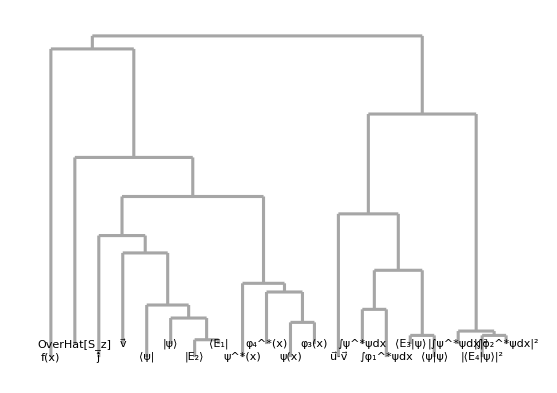

```mathematica
ConnectedGraphComponents[tlGraphs3[[150]]];
Length@ConnectedGraphComponents[tlGraphs3[[150]]];

(* initializes nComm as the number of disconnected subgraphs in the original, full network.  This will be updated in the loop to always be the current number of disconnected subgraphs *)
nComm=Length@ConnectedGraphComponents[tlGraphs3[[1]]];

(* redundant--I had forgotten that "num" was already used earlier for the number of edges *)
nEdges=EdgeCount[tlGraphs3[[1]]];
(* initializes splits as an empty list *)
splits={};

(* goes through the list of graphs as edges are removed, and adds the total number of removed edges at the point when a subgraph divides to the "splits" list.  This allows us to keep track of when the splits in the network occur, so we can more easily identify what spit off from where, and when that division occurs *)
For[i=1,i<=nEdges,i++,
j=nComm;
nComm=Length@ConnectedGraphComponents[tlGraphs3[[i]]];
If[j!=nComm,
splits=Append[splits,i]
]
]

(* initializes splitGraphs as an empty list, to be filled with the graphs *right before* being divided *)
splitGraphs={};
splitNumGraphs={};

(* goes through and fills splitGraphs with snapshots of the network, right before each split occurs *)
For[i=1,i<=Length@splits,i++,
splitGraphs=Append[
splitGraphs,
Show[
(* because we're using tlGraphs3, AND we're looking at the networks one step before they are divided, we can see the edge that will be removed in that step (they are highlighted in tlGraphs3) *)
tlGraphs3[[splits[[i]]-1]],
Graphics[Text[Style[ToString[splits[[i]]-1],FontSize->50,Bold]]]
]
];
splitNumGraphs=Append[
splitNumGraphs,
Show[
(* because we're using tlGraphs3, AND we're looking at the networks one step before they are divided, we can see the edge that will be removed in that step (they are highlighted in tlGraphs3) *)
tlGraphs3[[splits[[i]]-1]],
Graphics[Text[Style[ToString[i],FontSize->30,Bold]]]
]
]
]

(* required to have a vertex for each division point of the graph (nineteen), as well as each expression *)treeVerts={"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19",OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};



(* NEED TO GO THROUGH THE TREEEDGES AND FILL IN THE CORRECT LINKS FROM THE UPDATED DENDROGRAM *)




(* unfortunately, this is required to be filled out manually, by creating the dendrogram on paper, and noting when and where each division takes place.  Not fun. *)
treeEdges={treeVerts[[1]]<->treeVerts[[2]],treeVerts[[1]]<->treeVerts[[3]],treeVerts[[2]]<->treeVerts[[23]],treeVerts[[2]]<->treeVerts[[4]],treeVerts[[3]]<->treeVerts[[6]],treeVerts[[3]]<->treeVerts[[16]],treeVerts[[4]]<->treeVerts[[22]],treeVerts[[4]]<->treeVerts[[5]],treeVerts[[5]]<->treeVerts[[7]],treeVerts[[5]]<->treeVerts[[10]],treeVerts[[6]]<->treeVerts[[31]],treeVerts[[6]]<->treeVerts[[9]],treeVerts[[7]]<->treeVerts[[21]],treeVerts[[7]]<->treeVerts[[8]],treeVerts[[8]]<->treeVerts[[20]],treeVerts[[8]]<->treeVerts[[12]],treeVerts[[9]]<->treeVerts[[13]],treeVerts[[9]]<->treeVerts[[19]],treeVerts[[10]]<->treeVerts[[28]],treeVerts[[10]]<->treeVerts[[11]],treeVerts[[11]]<->treeVerts[[30]],treeVerts[[11]]<->treeVerts[[15]],treeVerts[[12]]<->treeVerts[[39]],treeVerts[[12]]<->treeVerts[[14]],treeVerts[[13]]<->treeVerts[[34]],treeVerts[[13]]<->treeVerts[[35]],treeVerts[[14]]<->treeVerts[[24]],treeVerts[[14]]<->treeVerts[[18]],treeVerts[[15]]<->treeVerts[[27]],treeVerts[[15]]<->treeVerts[[29]],treeVerts[[16]]<->treeVerts[[37]],treeVerts[[16]]<->treeVerts[[17]],treeVerts[[17]]<->treeVerts[[36]],treeVerts[[17]]<->treeVerts[[38]],treeVerts[[18]]<->treeVerts[[25]],treeVerts[[18]]<->treeVerts[[26]],treeVerts[[19]]<->treeVerts[[33]],treeVerts[[19]]<->treeVerts[[32]]};

(* defines the weights of the vertices (which Mathematica uses as the "heights" of the division points when the tree graph is converted to a dendrogram)  The +1 is required because "splits" doesn't include the final division (for some reason) *)
heightStagger=Join[nEdges-1-splits,{0,-2,-5,-2,-5,-2,-5,-2,-5,-5,-2,-2,-5,-5,-2,-2,-5,-5,-2,-2,-5}];
heightFlat=Join[nEdges-1-splits,{0},Table[-2,numVerts]];

TownsendTreeStagger=TreeGraph[treeVerts,treeEdges,VertexLabels->"Name",VertexWeight->heightStagger];
TownsendTreeFlat=TreeGraph[treeVerts,treeEdges,VertexLabels->"Name",VertexWeight->heightFlat];

Dendrogram[TownsendTreeStagger]/.Line[x_]:>{Thickness[0.005],Line[x]};
Dendrogram[TownsendTreeFlat]/.Line[x_]:>{Thickness[0.005],Line[x]};

Dendrogram[TownsendTreeStagger,ImageSize->800]/.Line[x_]:>{Thickness[0.004],Line[x]}

splitGraphs//MatrixForm;
```

## 7 Plotting networks

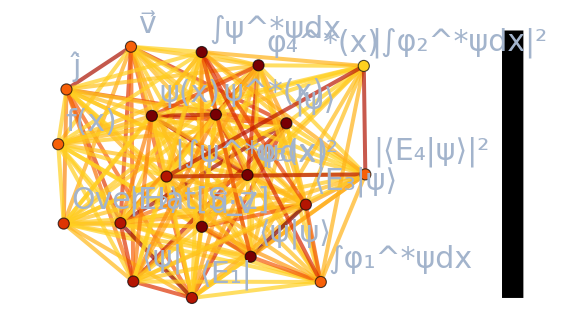

RGBColor[1., 0.820127, 0.126955]

RGBColor[0.468742, 0., 0.0158236]

```mathematica
Show[
tlGraphs2[[1]],
Graphics[
{Polygon[{{2.7,0},{2.83,0},{2.83,1.63},{2.7,1.63}},
VertexColors->{
Opacity[1,ColorData[{"SolarColors","Reverse"}][0]],
Opacity[1,ColorData[{"SolarColors","Reverse"}][0]],
Opacity[1,ColorData[{"SolarColors","Reverse"}][1]],
Opacity[1,ColorData[{"SolarColors","Reverse"}][1]]
}]}
]
]

ColorData[{"SolarColors","Reverse"}][0]
ColorData[{"SolarColors","Reverse"}][1]
```